```mathematica
n=1234567; PrimeQ[n]
```

False

```mathematica
n=16851;d=123;  IntegerQ[n/d]
```

True

```mathematica
n=16851; Divisors[n]
```

{1,3,41,123,137,411,5617,16851}

```mathematica
k=35; Prime[k]
```

149

```mathematica
k=2; Prime[k]
```

3

```mathematica
k=1; Prime[k]
```

2

```mathematica
n=17; PrimeQ[n]
```

True

```mathematica
n=100; PrimePi[n]
```

25

```mathematica
a=12345; b=67890; GCD[a,b]
```

15

```mathematica
FactorInteger[12345]
```

{{3,1},{5,1},{823,1}}

```mathematica
LCM[2,3]
```

6

```mathematica
findgcd[x_,y_]:=(
a=x;b=y;
While[b≠0, r=a-Floor[a/b]*b;{a,b}={b,r};Print[{a,b}]];Return[a])
```

```mathematica
findgcd[5,4]
```

{4,1}

{1,0}

1

```mathematica
findgcd[1645,861]
```

{861,784}

{784,77}

{77,14}

{14,7}

{7,0}

7

```mathematica
a=861; b=1645; ExtendedGCD[a,b]
```

{7,{107,-56}}

```mathematica
a=12345; m=7; Mod[a,m]
```

4

```mathematica
Table[Mod[8^i,17],{i,0,100}]
```

{1,8,13,2,16,9,4,15,1,8,13,2,16,9,4,15,1,8,13,2,16,9,4,15,1,8,13,2,16,9,4,15,1,8,13,2,16,9,4,15,1,8,13,2,16,9,4,15,1,8,13,2,16,9,4,15,1,8,13,2,16,9,4,15,1,8,13,2,16,9,4,15,1,8,13,2,16,9,4,15,1,8,13,2,16,9,4,15,1,8,13,2,16,9,4,15,1,8,13,2,16}

```mathematica
Table[Mod[7^i,16],{i,0,100}]
```

{1,7,1,7,1,7,1,7,1,7,1,7,1,7,1,7,1,7,1,7,1,7,1,7,1,7,1,7,1,7,1,7,1,7,1,7,1,7,1,7,1,7,1,7,1,7,1,7,1,7,1,7,1,7,1,7,1,7,1,7,1,7,1,7,1,7,1,7,1,7,1,7,1,7,1,7,1,7,1,7,1,7,1,7,1,7,1,7,1,7,1,7,1,7,1,7,1,7,1,7,1}

```mathematica
Table[Mod[5^i,18],{i,0,100}]
```

{1,5,7,17,13,11,1,5,7,17,13,11,1,5,7,17,13,11,1,5,7,17,13,11,1,5,7,17,13,11,1,5,7,17,13,11,1,5,7,17,13,11,1,5,7,17,13,11,1,5,7,17,13,11,1,5,7,17,13,11,1,5,7,17,13,11,1,5,7,17,13,11,1,5,7,17,13,11,1,5,7,17,13,11,1,5,7,17,13,11,1,5,7,17,13,11,1,5,7,17,13}

```mathematica
m=15; EulerPhi[m]
```

8

```mathematica
m=123456789; a= 1111111111;  GCD[m,a]
PowerMod[a, EulerPhi[m], m]
```

1

1

```mathematica
checkEulerT[x_,y_]:=(Print[GCD[x,y]];Print[EulerPhi[x]];Mod[y^EulerPhi[x],x])
```

```mathematica
Prime[100000]
checkEulerT[Prime[100000],11111]
```

1299709

1

1299708

1

```mathematica
checkEulerT[3,8]
```

1

2

1

```mathematica
checkEulerT[8,3]
```

1

4

1

```mathematica
checkEulerT[Prime[303]*Prime[302],Prime[301]*Prime[300]]
```

1

3988008

1

```mathematica
Prime[300]*Prime[301]
```

3960091

```mathematica
Prime[302]*Prime[303]
```

3992003

```mathematica
(Prime[303]-1)*(Prime[302]-1)
```

3988008

```mathematica
m=123456789; a= 1111111111;  GCD[m,a]
PowerMod[a, EulerPhi[m], m]
```

1

1

```mathematica
ExtendedGCD[Prime[200],Prime[201]]
```

{1,{-205,204}}

```mathematica
Prime[200]*(-205)+Prime[201]*204
```

1

```mathematica
ChineseRemainder[{2,3,4},{Prime[10],Prime[11],Prime[12]}]
```

1336

```mathematica
Mod[1336,Prime[10]]
```

2

```mathematica
Mod[1336,Prime[11]]
```

3

```mathematica
Mod[1336,Prime[12]]
```

4

```mathematica
u1=ChineseRemainder[{1,0,0},{13,29,64}]
```

7424

```mathematica
u2=ChineseRemainder[{0,1,0},{13,29,64}]
```

13312

```mathematica
u3=ChineseRemainder[{0,0,1},{13,29,64}]
```

3393

```mathematica
u1*10+u2*5+u3*7-13*29*64*6
```

19783

```mathematica
ChineseRemainder[{10,5,7},{13,29,64}]
```

19783

```mathematica
diffie_hellma
```

diffie_hellma

```mathematica
p = Prime[1000]
```

7919

```mathematica
a = 5
```

5

```mathematica
Xa = 76
```

76

```mathematica
Ya = Mod[a^76,p]
```

1200

```mathematica
cA=PowerMod[57766,56,Prime[10000]]
cB=PowerMod[57766,111,Prime[10000]]
```

30255

24601

```mathematica
PowerMod[cB,56,Prime[10000]]
```

42897

```mathematica
PowerMod[cA,111,Prime[10000]]
```

42897

```mathematica
gim
```

gim

```mathematica
mB=167
p=Prime[197];a=2;cB=PowerMod[a,mB,p];r=RandomInteger[{0,p-2}]
u=456;R=PowerMod[a,r,p]
S=Mod[PowerMod[cB,r,p] u,p]
Mod[S*PowerMod[PowerMod[R,mB,p],-1,p],p]
```

167

860

6

803

456

```mathematica
sig
```

sig

```mathematica
p=Prime[197];a=2;mA=376;r=Prime[100];u=456;S=.;R=PowerMod[a,r,p]
S=S/.Solve[{r *S==u-mA *R},{S},Modulus->p-1][[1]]
cA=PowerMod[a,mA,p];
PowerMod[a,u,p]==Mod[ PowerMod[cA,R,p]*PowerMod[R,S,p],p]
```

210

456

True

```mathematica
pB=Prime[1300]
qB=Prime[1450]
nB=pB*qB
phiB=EulerPhi[nB]
eB=RandomInteger[{1,nB}];
While[GCD[eB,phiB]≠1,eB=RandomInteger[{1,nB}]];
{x1,{dB,x3}}=ExtendedGCD[eB,phiB]
Mod[eB*dB,phiB]
m=12345678;
c=PowerMod[m,eB,nB]
PowerMod[c,dB,nB]
```

10657

12109

129045613

129022848

{1,{-4263145,543942}}

1

48279435

12345678

```mathematica
RSA
```

RSA

```mathematica
pB1=Prime[1300]
qB1=Prime[1450]
nB1=pB1*qB1
phiB1=EulerPhi[nB1]
eB1=RandomInteger[{1,nB1}];
While[GCD[eB1,phiB1]≠1,eB1=RandomInteger[{1,nB1}]];
{x1,{dB1,x3}}=ExtendedGCD[eB1,phiB1]
Mod[eB1*dB1,phiB1]
pB2=Prime[1301]
qB2=Prime[1451]
nB2=pB2*qB2
phiB2=EulerPhi[nB2]
eB2=RandomInteger[{1,nB2}];
While[GCD[eB2,phiB2]≠1,eB2=RandomInteger[{1,nB2}]];
{x1,{dB2,x3}}=ExtendedGCD[eB2,phiB2]
Mod[eB2*dB2,phiB2]
m=12345678;
c=PowerMod[PowerMod[m,eB1,nB1],dB2,nB2]
PowerMod[PowerMod[c,eB2,nB2],dB1,nB1]
```

10657

12109

129045613

129022848

{1,{13744115,-12317993}}

1

10663

12113

129160919

129138144

{1,{-28607149,7034788}}

1

27175278

12345678

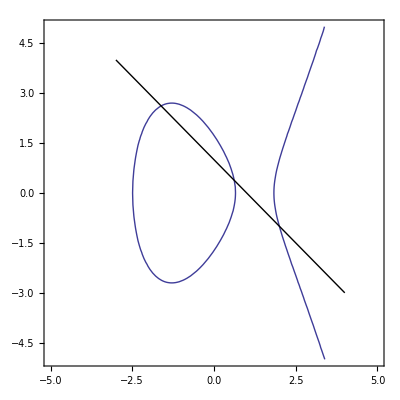

```mathematica
elliptic=ContourPlot[y^2==x^3-5 x+3,{x,-5,5},{y,-5,5},Axes->True,Epilog->Line[{{-3,4},{4,-3}}]]
```

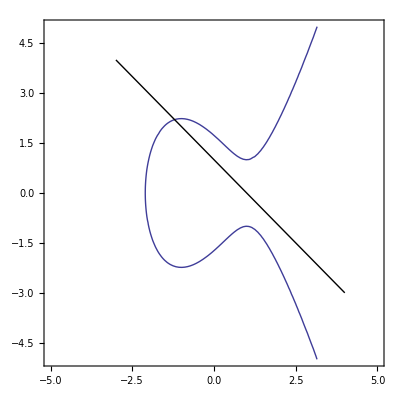

```mathematica
elliptic=ContourPlot[y^2==x^3-3x+3,{x,-5,5},{y,-5,5},Axes->True,Epilog->Line[{{-3,4},{4,-3}}]]
```

```mathematica
Manipulate[ContourPlot[y^2==x^3+n*x+3,{x,-5,5},{y,-5,5},Axes->True,Epilog->Line[{{-3,4},{4,-3}}]],{n,-5,-3,1}]
```

```mathematica
NSolve[ {y^2==x^3-5 x+3,y==-x+1},{x,y}]
```

{{x→-1.61803,y→2.61803},{x→2.,y→-1.},{x→0.618034,y→0.381966}}

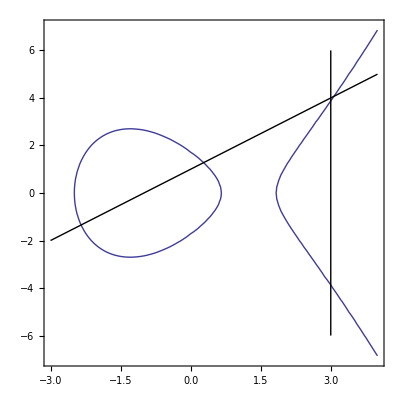

```mathematica
elliptic=ContourPlot[y^2==x^3-5 x+3,{x, -3,4},{y,-7,7},Axes->True,Epilog->{Line[{{3,6},{3,-6}}],Line[{{-3,-2},{4,5}}]}]
```

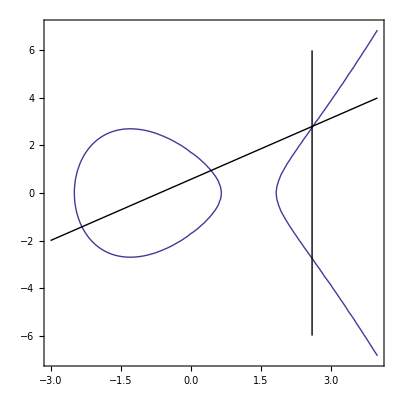

```mathematica
elliptic=ContourPlot[y^2==x^3-5 x+3,{x, -3,4},{y,-7,7},Axes->True,Epilog->{Line[{{2.6,6},{2.6,-6}}],Line[{{-3,-2},{4,4}}]}]
```

```mathematica
NSolve[ {y^2==x^3-5 x+3,y==-x+1},{x,y}]
```

{{x→-1.61803,y→2.61803},{x→2.,y→-1.},{x→0.618034,y→0.381966}}

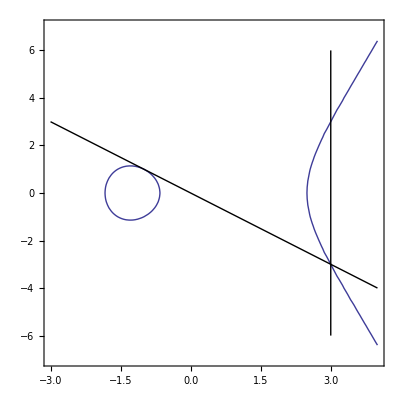

```mathematica
elliptic=ContourPlot[y^2==x^3-5 x-3,{x, -3,4},{y,-7,7},Axes->True,Epilog->{Line[{{3,6},{3,-6}}],Line[{{-3,3},{4,-4}}]}]
```

```mathematica
Clear[x,y]; 
p=11;
Flatten[Table[ Solve[ {y^2== x^3-5 x + 3, x==u},{x,y}, Modulus->p], {u, 0, p-1}] ,1]
```

{{x→0,y→5},{x→0,y→6},{x→2,y→1},{x→2,y→10},{x→3,y→2},{x→3,y→9},{x→4,y→5},{x→4,y→6},{x→5,y→2},{x→5,y→9},{x→7,y→5},{x→7,y→6},{x→9,y→4},{x→9,y→7}}

```mathematica
Clear[x,y]; 
p=11;
Table[ Solve[ {y^2== x^3-5 x + 3, x==u},{x,y}, Modulus->p], {u, 0, p-1}]
```

{{{x→0,y→5},{x→0,y→6}},{},{{x→2,y→1},{x→2,y→10}},{{x→3,y→2},{x→3,y→9}},{{x→4,y→5},{x→4,y→6}},{{x→5,y→2},{x→5,y→9}},{},{{x→7,y→5},{x→7,y→6}},{},{{x→9,y→4},{x→9,y→7}},{}}

```mathematica
NSolve[ {y^2==x^3-5 x+3,y==-x+1},{x,y}]
```

{{x→-1.61803,y→2.61803},{x→2.,y→-1.},{x→0.618034,y→0.381966}}

```mathematica
p=11;Solve[ {y^2==x^3-5 x+3,y==x- 1},{x,y},Modulus-> p]
```

{{x→2,y→1},{x→3,y→2},{x→7,y→6}}

```mathematica
InterpolatingPolynomial[{{0,5},{2,10}},v1]
```

5+(5 v1)/2

```mathematica
p=11;Solve[ {y^2==x^3-5 x+3,y==5+(5 x)/2},{x,y},Modulus-> p]
```

{{x→0,y→5},{x→2,y→10},{x→7,y→6}}

```mathematica
EllipticAdd[p_, a_, b_, c_, P_List, Q_List] := 
 Module[{lam, x3, y3, P3},
   Which[ P == {O}, R = Q,
          Q == {O}, R = P,
          P[[1]] != Q[[1]],		  
            lam = Mod[(Q[[2]] - P[[2]]) PowerMod[Q[[1]] - P[[1]], -1, p], p];
            x3 = Mod[lam^2 - a - P[[1]] - Q[[1]], p];
            y3 = Mod[-(lam (x3 - P[[1]]) + P[[2]]), p];
            R = {x3, y3},
         (P == Q) && (P != {O}),
            lam = Mod[(3*P[[1]]^2 + 2 a*P[[1]] + b)
                      PowerMod[2 P[[2]], -1, p], p];
            x3 = Mod[lam^2 - a - P[[1]] - Q[[1]], p];
            y3 = Mod[-(lam (x3 - P[[1]]) + P[[2]]), p];
            R = {x3, y3},
         (P[[1]] == Q[[1]]) && (P[[2]] != Q[[2]]),
            R = {O}
        ]; R
       ]
```

```mathematica
EllipticAdd[11,0,-5,3,{0,5},{2,10}]
```

{7,5}

```mathematica
p=11;Solve[ {y^2==x^3-5 x+3,y==InterpolatingPolynomial[{{0,5},{2,10}},x]},{x,y},Modulus-> p]
```

{{x→0,y→5},{x→2,y→10},{x→7,y→6}}

```mathematica
p=863;P=.;
a=100;b=10;c=1;
P[0]={121,517};
P[i_] := P[i] = EllipticAdd[p,a,b,c,P[i-1],P[i-1]];		 
QAlice=EllipticAdd[p,a,b,c,P[9],P[1]]
QBob=EllipticAdd[p,a,b,c,P[8],P[4]]
QA[0]={341,688};QA[i_]:=QA[i]=EllipticAdd[p,a,b,c,QA[i-1],QA[i-1]];EllipticAdd[p,a,b,c,QA[9],QA[1]]
QB[0]={162,663};QB[i_]:=QB[i]=EllipticAdd[p,a,b,c,QB[i-1],QB[i-1]];EllipticAdd[p,a,b,c,QB[8],QB[4]]
```

{577,250}

{533,251}

{341,688}

{572,41}

```mathematica
p=863;P=.;
a=100;b=10;c=1;
P[0]={121,517};
P[i_] := P[i] = EllipticAdd[p,a,b,c,P[i-1],P[i-1]];
Q=EllipticAdd[p,a,b,c,EllipticAdd[p,a,b,c,P[8],P[7]],		 EllipticAdd[p,a,b,c,P[5],P[4]]]
EllipticAdd[p,a,b,c,EllipticAdd[p,a,b,c,P[7],P[6]],	 	EllipticAdd[p,a,b,c,P[4],P[3]]]
EllipticAdd[p,a,b,c,P[7],P[4]]
```

{O}

{19,0}

{341,175}

```mathematica
IntegerDigits[130,2]
```

{1,0,0,0,0,0,1,0}

```mathematica
IntegerDigits[288,2]
```

{1,0,0,1,0,0,0,0,0}

```mathematica
IntegerDigits[432,2]
```

{1,1,0,1,1,0,0,0,0}

```mathematica
p=863;P=.;
a=100;b=10;c=1;
P[0]={121,517};
P[i_] := P[i] = EllipticAdd[p,a,b,c,P[i-1],P[i-1]];
```

```mathematica
Table[P[n],{n,1,20,1}]
```

{{630,588},{447,354},{69,852},{348,843},{539,467},{572,822},{124,198},{804,143},{363,372},{533,612},{579,214},{790,469},{348,20},{539,396},{572,41},{124,665},{804,720},{363,491},{533,251},{579,649}}

```mathematica
IntegerDigits[432,2]
```

{1,1,0,1,1,0,0,0,0}

```mathematica
p=863;P=.;
a=100;b=10;c=1;
P[0]={121,517};
P[i_] := P[i] = EllipticAdd[p,a,b,c,P[i-1],P[i-1]];
Q=EllipticAdd[p,a,b,c,EllipticAdd[p,a,b,c,P[8],P[7]],		 EllipticAdd[p,a,b,c,P[5],P[4]]]
```

{O}

```mathematica
Prime[100]
```

541

```mathematica
p=863
```

863

```mathematica
p=863;a=100;b=10;c=1;x=121;y=517;Mod[y^2-(x^3+a*x^2+b*x+c),p]==0
```

True

```mathematica
p=863;P=.;
a=100;b=10;c=1;
P[0]={121,541};
P[i_] := P[i] = EllipticAdd[p,a,b,c,P[i-1],P[i-1]];
Q=EllipticAdd[p,a,b,c,EllipticAdd[p,a,b,c,P[8],P[7]],		 EllipticAdd[p,a,b,c,P[5],P[4]]]
EllipticAdd[p,a,b,c,EllipticAdd[p,a,b,c,P[7],P[6]],	 	EllipticAdd[p,a,b,c,P[4],P[3]]]
EllipticAdd[p,a,b,c,P[7],P[4]]
```

{O}

{19,0}

{341,175}

```mathematica
{539,396}
```

{539,396}

```mathematica
p=863;a=100;b=10;c=1;x=539;y=396;Mod[y^2-(x^3+a*x^2+b*x+c),p]==0
```

True

```mathematica
p=863;P=.;
a=100;b=10;c=1;
P[0]={539,396};
P[i_] := P[i] = EllipticAdd[p,a,b,c,P[i-1],P[i-1]];		 
QAlice=EllipticAdd[p,a,b,c,P[7],P[5]]
QBob=EllipticAdd[p,a,b,c,P[8],P[5]]
QA[0]=QBob;QA[i_]:=QA[i]=EllipticAdd[p,a,b,c,QA[i-1],QA[i-1]];EllipticAdd[p,a,b,c,QA[7],QA[5]]
QB[0]=QAlice;QB[i_]:=QB[i]=EllipticAdd[p,a,b,c,QB[i-1],QB[i-1]];EllipticAdd[p,a,b,c,QB[8],QB[5]]
```

{533,612}

{341,688}

{341,688}

{341,688}

```mathematica
Z2mEllipticAdd[a_, c_, P_List, Q_List] := 
 Module[{lam, x3, y3, P3,R},
   Which[ P == {O}, R = Q,
          Q == {O}, R = P,
          ToElementCode[P[[1]]] != ToElementCode[Q[[1]]],
            lam = (Q[[2]] + P[[2]])/(Q[[1]] + P[[1]]);
            x3 = lam^2 + lam + a + P[[1]] + Q[[1]];
            y3 = lam (x3 + P[[1]]) + x3 + P[[2]];
            R = {x3, y3},
         ((ToElementCode[P[[1]]] == ToElementCode[Q[[1]]]) && 
          (ToElementCode[P[[2]]] == ToElementCode[Q[[2]]])) &&
         (P != {O}),
            lam = P[[1]] + P[[2]]/P[[1]];
            x3 = lam^2 + lam + a;
            y3 = P[[1]]^2 + (lam + 1) x3;
            R = {x3, y3},
         (ToElementCode[P[[1]]] == ToElementCode[Q[[1]]]) &&
	 (ToElementCode[P[[2]]] != ToElementCode[Q[[2]]]),
            R = {O}
        ]; R
       ]
```

```mathematica
<<FiniteFields`
```

```mathematica
z16 = GF[2,4]
```

GF[2,{1,0,0,1,1}]

```mathematica
FullForm[%]
```

GF[2,List[1,0,0,1,1]]

```mathematica
FieldIrreducible[z16,x]
```

FieldIrreducible[GF[2,{1,0,0,1,1}],539]

```mathematica
Characteristic[z16]
```

2

```mathematica
ExtensionDegree[z16]
```

4

```mathematica
FieldSize[z16]
```

16

```mathematica
dd =z16[{0,0,1,1}]
```

{0,0,1,1}_2

```mathematica
ee = z16[{1,1,0,0}]
```

{1,1,0,0}_2

```mathematica
dd/ee
```

{0,0,1,0}_2

```mathematica
dd+dd
```

0

```mathematica
dd-dd
```

0

```mathematica
dd+ee
```

{1,1,1,1}_2

```mathematica
dd-ee
```

{1,1,1,1}_2

```mathematica
Table[dd^n,{n,0,15,1}]
```

{1,{0,0,1,1}_2,{0,1,1,0}_2,{1,1,0,0}_2,{1,0,1,1}_2,{0,1,0,1}_2,{1,0,1,0}_2,{0,1,1,1}_2,{1,1,1,0}_2,{1,1,1,1}_2,{1,1,0,1}_2,{1,0,0,1}_2,{0,0,0,1}_2,{0,0,1,0}_2,{0,1,0,0}_2,{1,0,0,0}_2}

```mathematica
Table[(dd^n)^3+ee*(dd^n)^2,{n,0,15,1}]
```

{{0,1,0,0}_2,{1,0,0,1}_2,{1,1,0,1}_2,0,{1,0,0,0}_2,{1,0,1,0}_2,{0,1,0,0}_2,{1,1,0,0}_2,{0,1,0,0}_2,{1,0,1,1}_2,{0,1,1,0}_2,{0,0,0,1}_2,{1,0,1,1}_2,{1,0,1,1}_2,{0,0,1,0}_2,{0,1,0,0}_2}

```mathematica
(dd^3)^3+ee*(dd^3)^2
```

0

```mathematica
x=dd^3
```

{1,1,0,0}_2

```mathematica
y=x
```

{1,1,0,0}_2

```mathematica
Z2mEllipticAdd[a_, c_, P_List, Q_List] := 
 Module[{lam, x3, y3, P3,R},
   Which[ P == {O}, R = Q,
          Q == {O}, R = P,
          ToElementCode[P[[1]]] != ToElementCode[Q[[1]]],
            lam = (Q[[2]] + P[[2]])/(Q[[1]] + P[[1]]);
            x3 = lam^2 + lam + a + P[[1]] + Q[[1]];
            y3 = lam (x3 + P[[1]]) + x3 + P[[2]];
            R = {x3, y3},
         ((ToElementCode[P[[1]]] == ToElementCode[Q[[1]]]) && 
          (ToElementCode[P[[2]]] == ToElementCode[Q[[2]]])) &&
         (P != {O}),
            lam = P[[1]] + P[[2]]/P[[1]];
            x3 = lam^2 + lam + a;
            y3 = P[[1]]^2 + (lam + 1) x3;
            R = {x3, y3},
         (ToElementCode[P[[1]]] == ToElementCode[Q[[1]]]) &&
	 (ToElementCode[P[[2]]] != ToElementCode[Q[[2]]]),
            R = {O}
        ]; R
       ]
```

```mathematica
x=dd^3
Subscript[{1,1,0,0}, 2]
y=x
Subscript[{1,1,0,0}, 2]
a=ee;c=0;
P[0]={x,y};
P[i_] := P[i] = Z2mEllipticAdd[a,c,P[i-1],P[i-1]];
```

```mathematica
PDoubles=Table[P[n],{n,0,31,1}]
```